/Users/macmjrt

1/((-1.2+1/z) ((0.+1.2 ⅈ)+1/z) (-1.2+z) ((0.-1.2 ⅈ)+z))

ⅇ^(1/z)+ⅇ^z

{Listable}

Power::infy: Infinite expression 1/(0.+0. ⅈ) encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

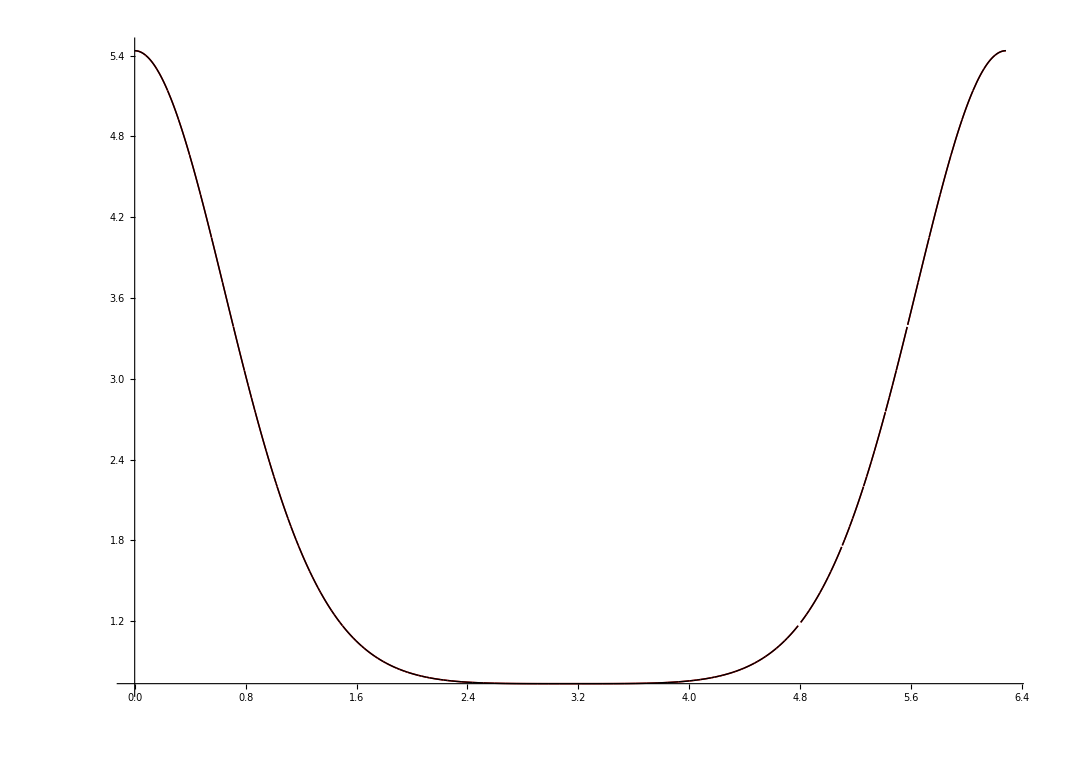

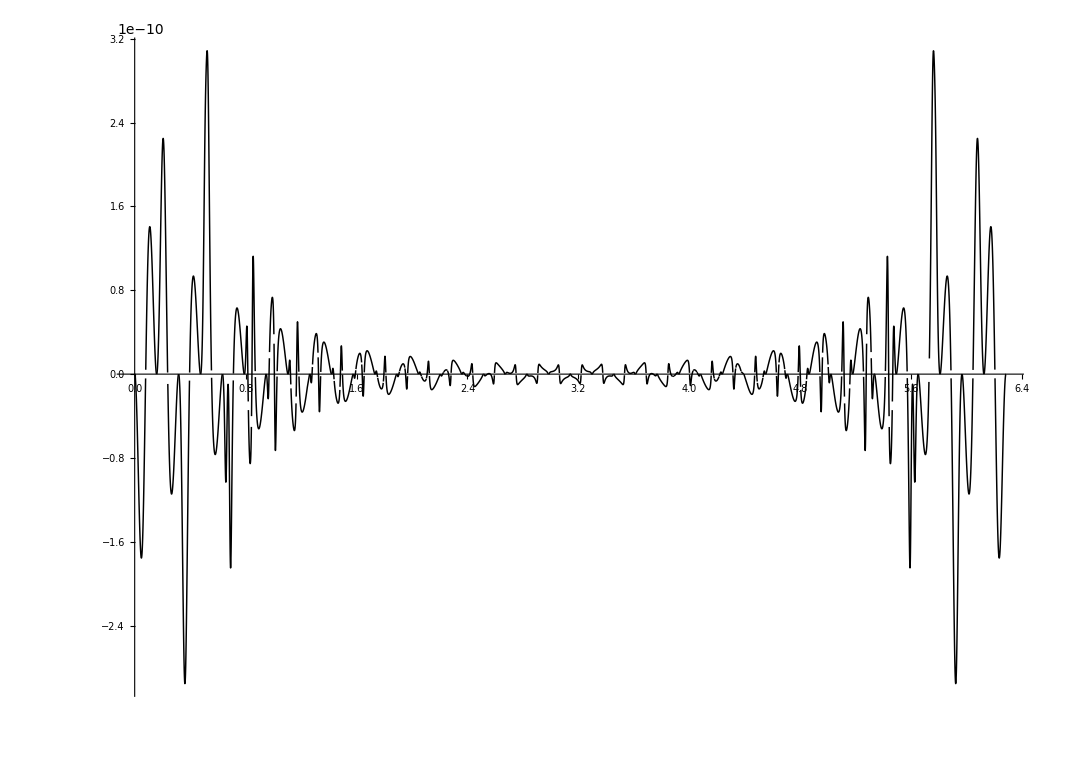

```mathematica
directorio=Directory[]



ftest[z_]=1/((z-1.2)(1/z-1.2)(z-1.2I)(1/z-1.2/I))
ftest[z_]=Exp[z]+Exp[1/z]


Attributes[ftest]={Listable}



(* kepler.wls obtains the system of arcs related with the satellite position and write it as arcosalpha *)

n=40;T=2*Pi;

Get["Dropbox/articulo2023/kepler.wls"]



(* arcos.wls obtains all the system of arcs related with arcosalpha in the sense of the paper and the related nodal systems *)
Get["Dropbox/atypeofinterpolation2023/arcos.wls"]



(* derivadas.wls obtains the derivatives used in the paper for a nodal system in T *)
listaalpha=alphaW2n;listaarcosalpha=arcosalphaW2n;
Get["Dropbox/atypeofinterpolation2023/derivadas.wls"];
derivadasalphaW2n=derivadas;
derivadassegundasalphaW2n=derivadas*factoresderivadassegundas;

(* same comment as before *)
listaalpha=alphaYn;listaarcosalpha=arcosalphaYn;
Get["Dropbox/atypeofinterpolation2023/derivadas.wls"];
derivadasalphaYn=derivadas;
derivadassegundasalphaYn=derivadas*factoresderivadassegundas;




(* same comment as before *)
listaalpha=alphaZn;listaarcosalpha=arcosalphaZn;
Get["Dropbox/atypeofinterpolation2023/derivadas.wls"];
derivadasalphaZn=derivadas;
derivadassegundasalphaZn=derivadas*factoresderivadassegundas;

(* u and v in the sense of the paper *)
u=N[ftest[alphaW2n],50];v=N[ftest'[alphaW2n],50];

(* semi Hermite and semi Hermite-Fejer interpolants using the barycentric formulae *)



SHerm[z_]=(∑_(k=1)^n ((alphapwp[[2k]]derivadasalphaZn[[k]]u[[2k]])/((z-alphaW2n[[2k]])(derivadasalphaW2n[[2k]])^2)+alphapwp[[2k-1]]/((z-alphaW2n[[2k-1]])derivadasalphaW2n[[2k-1]]derivadasalphaYn[[k]]) (1/(z-alphaW2n[[2k-1]])-derivadassegundasalphaW2n[[2k-1]]/(2 derivadasalphaW2n[[2k-1]])-derivadassegundasalphaYn[[k]]/(2 derivadasalphaYn[[k]])+(3n)/2)u[[2k-1]])+∑_(k=1)^n (alphapwp[[2k-1]]/((z-alphaW2n[[2k-1]])derivadasalphaW2n[[2k-1]]derivadasalphaYn[[k]])v[[2k-1]]))/(∑_(k=1)^n ((alphapwp[[2k]]derivadasalphaZn[[k]])/((z-alphaW2n[[2k]])(derivadasalphaW2n[[2k]])^2)+alphapwp[[2k-1]]/((z-alphaW2n[[2k-1]])derivadasalphaW2n[[2k-1]]derivadasalphaYn[[k]]) (1/(z-alphaW2n[[2k-1]])-derivadassegundasalphaW2n[[2k-1]]/(2 derivadasalphaW2n[[2k-1]])-derivadassegundasalphaYn[[k]]/(2 derivadasalphaYn[[k]])+(3n)/2)));





BB=Plot[{Re[SHerm[E^(I x)]],Re[ftest[E^(I x)]]},{x,0,2Pi}, PlotRange->Full,PlotPoints->600,PlotStyle->{{Red,Thickness[.001]},{Black,Thickness[.001]}},AspectRatio->5/7];
BB1=Plot[{Re[SHerm[E^(I x)]]-Re[ftest[E^(I x)]]},{x,0,2Pi}, PlotRange->Full,PlotPoints->200,PlotStyle->{{Black,Thickness[.001]},{Black,Thickness[.001]}},AspectRatio->5/7];




(*AA=Table[{Re[Log[alphaW2n[[k]]]/I],Re[ftest[alphaW2n[[k]]]]},{k,1,3n/4}];
AA=ListPlot[AA,PlotStyle->PointSize[.005]];*)
Show[BB]
Show[BB1]
```